```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
qpData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,qpData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,invX_ :True]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
If[invX,x=1/Sqrt[x]];
result=Table[{x[[it]],y[[it]]},{it,Length[x]}];
Clear[x,y];
result
)
```

```mathematica
makeFits[data_,func_,arg_,points_]:=Table[Fit[d[[-Min[points,Length[d]];;-1]],func,arg],{d, data}];
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getPlot[data_,func_, arg_,points_]:=(
SetOptions[LinTicks,TickLengthScale->2.5];
SetOptions[MaTeX,Magnification->1.8];

label=If[k==0.0,"(d)",If[k==0.5,"(b)",If[k==1.0,"(f)",""]]];
klabel="";(*If[k==0.0,"k=0",If[k==0.5,"k=\\pi/2",If[k==1.0,"k=\\pi",""]]];*)

colors={Black};
(*Table[If[B<=1.0,Blend[{Purple,Orange},1-Sqrt[1-B]],Blend[{Red,Blue},1-Sqrt[B-1]]],{B,qpAvail["interaction"]//Normal}];*)
pltStyle=Table[Directive[Dashed,color,Opacity[0.7]],{color,colors}];

fs=22;
plt=ListPlot[data,
PlotRange->{{-0.5,2.0001},{0,0.2}},ImageSize->360,
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotMarkers->{"●", 14},
(*
PlotLegends->If[k==0.0,Placed[
PointLegend[Table[
MaTeX[StringJoin["\\lambda = ",ToString[NumberForm[B,{2,1}]]],Magnification->1.55],
{B,qpAvail["interaction"]//Normal}],Spacings->0.0],
{0.5,0.85}],None],
*)
(*Epilog->{
Inset[
MaTeX["\\text{"<>label<>" }"],
Scaled[{-0.187,1.05}]],
Inset[
MaTeX[klabel],
Scaled[{0.25,0.8}]]
},*)
FrameLabel->{MaTeX["\\lambda"],MaTeX["z"]},
LabelStyle->Directive[Black,12],
PlotStyle->pltStyle,
AspectRatio->.75,
FrameTicks->{{LinTicks[0,0.2,0.05,5,TickLabelFunction->tlf],StripTickLabels[LinTicks[0,0.2,0.05,5]]},{LinTicks[-0.5,2.0,0.5, 10,TickLabelFunction->tlf],StripTickLabels[LinTicks[-0.5,2.0,0.5, 10]]}}
];

(*fits=makeFits[data,func,arg,points];
fplt=Plot[fits,{x,0,0.3},PlotStyle->pltStyle];*)

Show[plt,PlotRangeClipping->False]
)
```

```mathematica
makePlotsZ[]:=(
fitFunctions={1,x, x^2};
fitPoints=11;

directive={Select[#coupling==J&&#momentum==k&]};
keys={"interaction","weight"};

plots={};
Do[(
Do[(
z={};
AppendTo[z,extractData[qpDataset,directive,keys,False]];
AppendTo[plots,{getPlot[z,fitFunctions, x,fitPoints]}];
),{k,qpAvail["momentum"]//Normal}];
),{J,qpAvail["coupling"]//Normal}];

plots
)
```

J ∈ {0.4} @ 16-2-16_-0.5-0.1-2.0

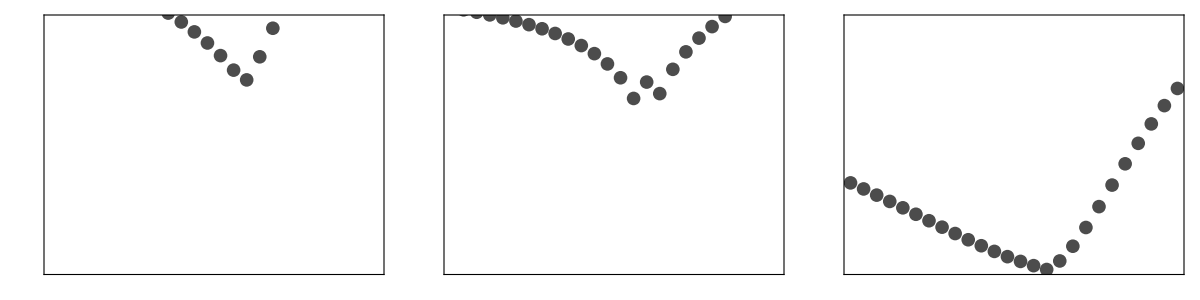

```mathematica
JRange={"0.4"};
tails={"16-2-16_-0.5-0.1-2.0"};
(*tails={"12-2-28_0.5-0.4-0.9","12-2-28_1.1-0.1-1.1"};*)
zPlots={};
Do[(
qpDataset=Dataset[getAssoc["qp",JRange,tail]];
qpAvail=Dataset[getStruct[qpDataset]];
Print[Style[StringJoin["J ∈ ",ToString[JRange]," @ ", tail],16]];
AppendTo[zPlots,makePlotsZ[]];
kDim=Length[qpAvail["momentum"]];
plots=ArrayReshape[zPlots[[-1]],{Length[zPlots[[-1]]]/kDim,kDim}];
Print[Grid[plots]];
),{tail,tails}]
```

```mathematica
(*SavePlots[]:=(
Do[(
Do[(
fileName=StringJoin["plots/scaling/z/",
"z_J=",ToString[qpAvail["coupling"][[iJ]]],
"_k=",ToString[qpAvail["momentum"][[ik]]],
".jpg"];
Export[fileName,zPlots[[1,(iJ-1)*Length[qpAvail["momentum"]//Normal]+ik,1]],ImageResolution->300];
),{ik,Length[qpAvail["momentum"]//Normal]}]
),{iJ,Length[qpAvail["coupling"]//Normal]}]
)*)
```

```mathematica
(*SavePlots[]*)
```

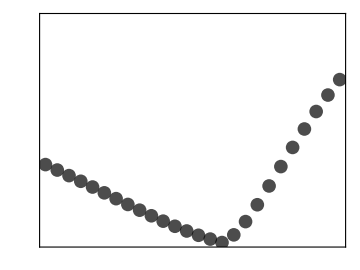

```mathematica
zPts=Table[Show[zPlots[[;;,l,1]]],{l,{3}}]
```

```mathematica
(*jointPts=Grid[Table[{gapPts[[it]],zPts[[it]]},{it,{1,2,3}}]//Transpose,Spacings->-0.2]*)
```

```mathematica
(*Export["/Users/pwrzosek/Desktop/spin_polaron_figs/fig5b.png",zPts[[2]],ImageResolution->300];*)
```

```mathematica
mydata=Select[qpDataset,#momentum==1.0&][Take,{"interaction","weight"}]
```

```mathematica
mydata[1;;11]
```

```mathematica
int=mydata[1;;11][Take,"interaction"]//Normal
weight=mydata[1;;11][Take,"weight"]//Normal
```

{0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.}

{0.00648787,0.00577747,0.00508432,0.0044076,0.00374553,0.00309465,0.00244816,0.00179287,0.00110772,0.000404683,1.11704×10^-31}

```mathematica
mypairs=Table[{int[[i]],weight[[i]]},{i,1,11}]
```

{{0.8,0.00648787},{0.82,0.00577747},{0.84,0.00508432},{0.86,0.0044076},{0.88,0.00374553},{0.9,0.00309465},{0.92,0.00244816},{0.94,0.00179287},{0.96,0.00110772},{0.98,0.000404683},{1.,1.11704×10^-31}}

```mathematica
line=Fit[mypairs,{1,x},x]
```

0.0327357-0.0329032 x

```mathematica
c = Normal[mydata[1;;1]][[1,2]]
```

0.00648787

```mathematica
line=-c(x-1)
```

-0.00648787 (-1+x)

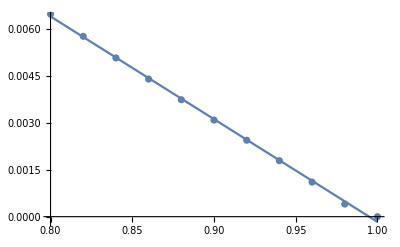

```mathematica
Show[Plot[line,{x,0.8,1}],ListPlot[mydata]]
```

```mathematica
FindFormula[mypairs,x,5]
```

{0.0327357-0.0329032 x,0.697053+0.00668357 0.098024^(1/x^24) 0.808045^x-0.378079 x-0.0248611 x^5-0.545344 Cos[x],Log[x],Log[Abs[x]],0.202416 x Cot[x]}

```mathematica
mypairs
```

{{0.8,0.00648787},{0.82,0.00577747},{0.84,0.00508432},{0.86,0.0044076},{0.88,0.00374553},{0.9,0.00309465},{0.92,0.00244816},{0.94,0.00179287},{0.96,0.00110772},{0.98,0.000404683},{1.,1.11704×10^-31}}